# Практикум по квантовой химии твердого тела

Нехаев А.С.

Гагин А.А.

Ноябрь 2020

МФТИ

Введение

Ab initio расчеты электронной структуры твердого тела в настоящее время широко применяются для прогнозирования устойчивости соединений, оценки их реакционной способности,предсказания транспортных и магнитных свойств. В настоящей практической работе Вам будет предложено провести модельное исследование фазового перехода под высоким давлением с одновременной оценкой электронных свойств фаз.

## Постановка задачи

Оксид титана может кристаллизоваться в нескольких полиморфных модификациях (рутил, анатаз, брукит), отличающихся пространственной упаковкой октаэдров  TiO_2. Различные типы упаковки приводят к отличиям в плотности фаз. Так, кристаллографическая (т.е. рассчитанная из объема элементарной ячейки, массы формульной единицы и числа формульных единиц в ячейке) плотность рутила составляет 4.250 г/см^3, а анатаза - 3.893 г/см^3. В условиях приложения высокого давления энтальпия реакции

TiO_2 (анатаз)<-> TiO_2 (рутил)

будет уменьшаться (ΔH = ΔU + pΔV, ΔV < 0), что, с учетом минимального энтропийного вклада (S_анатаз ≈ S_рутил, Δ S≈0) приведет к обязательному уменьшению ΔG реакции с ростом давления вплоть до отрицательных величин. Это соответствует смещению равновесия в сторону рутила при повышенном давлении.

Цель данной работы заключается в теоретическом описании изменений, происходящих в системе анатаз-рутил при приложении высокого давления.

В данной работе решаются следующие задачи:

Расчет электронной сигнатуры анатаза и рутила для нескольких значений объема элементарной ячейки;

Построение зависимостей E_tot(V) для обеих фаз, определение равновесного значения V и упругих постоянных;

Определение давления перехода анатаз-рутил (Построение зависимости ΔH(P));

Исследование зависимости E_g(P) для обеих фаз;

## Расчеты

На удаленном кластере проводим расчеты для анатаза и рутила. При этом используем структурные данные приведенные в практикуме:

Анатаз

Пространственная группа (Space Group) | I4_1/amd (№141)
Параметры элементарной ячейки (Lattice constant) | 3.771Å,3.771 Å,9.430 Å
Углы в элементарной ячейке | 90,90,90
Количество независимых атомов (Number of atoms) | 2
Координаты атомов | Ti 0.0,0.25,0.375
O 0.0,0.25,0.1656

Рутил

Пространственная группа (Space Group) | P4_2/mnm (№136)
Параметры элементарной ячейки (Lattice constant) | 4.585Å,4.585 Å,2.953 Å
Углы в элементарной ячейке | 90,90,90
Количество независимых атомов (Number of atoms) | 2
Координаты атомов | Ti 0.0,0.0,0.0
O 0.3049,0.3049,0.0

Мы проводим расчеты для различных объемов ячейки в интервале объемов от 0.94 V_0 до 1.01 V_0 с шагом 1%. За V_0 принимаются значения размеров элементарной ячейки. В матрице ниже представлены размеры рассчиываемых объемов для анатаза:

```mathematica
params=({{3.771, 3.771, 9.430}});
volCoefs={Range[0.94,1.01,0.01]};
Transpose[(∏_(i=1)^3 params[[1,i]])*volCoefs]//MatrixForm
```

(126.053
127.394
128.735
130.076
131.417
132.758
134.099
135.44)

Размеры соответствующих ячеек:

```mathematica
Transpose[volCoefs^(1/3)].params//MatrixForm
```

(3.69402 | 3.69402 | 9.2375
3.70707 | 3.70707 | 9.27014
3.72003 | 3.72003 | 9.30255
3.73291 | 3.73291 | 9.33474
3.74569 | 3.74569 | 9.36671
3.75839 | 3.75839 | 9.39846
3.771 | 3.771 | 9.43
3.78353 | 3.78353 | 9.46133)

Аналогично считаем объемы для рутила:

```mathematica
params2=({{4.585, 4.585, 2.953}});
Transpose[(∏_(i=1)^3 params2[[1,i]])*volCoefs]//MatrixForm
```

(58.3539
58.9747
59.5955
60.2163
60.8371
61.4578
62.0786
62.6994)

И размеры его ячеек:

```mathematica
Transpose[volCoefs^(1/3)].params2//MatrixForm
```

(4.4914 | 4.4914 | 2.89272
4.50727 | 4.50727 | 2.90294
4.52303 | 4.52303 | 2.91309
4.53868 | 4.53868 | 2.92317
4.55423 | 4.55423 | 2.93318
4.56967 | 4.56967 | 2.94312
4.585 | 4.585 | 2.953
4.60023 | 4.60023 | 2.96281)

Используя полученные параметры проводим расчеты согласно описанию, данному в практикуме.

## Определение объемного модуля упругости образцов

По полученным результатам мы можем получить зависимость полной энергии E(V). Учитываем, что полная энергия приводится к примитивной ячейке, а рассчитанный объем соотвествует кристаллографической ячейке, поэтому параметры необходимо приводить к одной формульной единице TiO_2. Для этого в случае анатаза нужно использовать формулы (1)

EE_1=EE/2, V_1=V/4,

а для рутила (2)

EE_1=EE/2, V_1=V/2.

Строим данные зависимости по результатам расчетов и аппроксимируем точки кривой второго порядка.

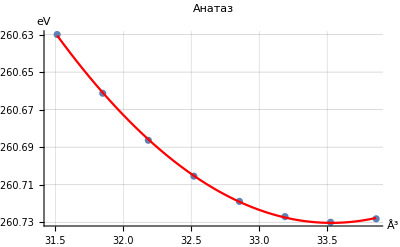

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["fplo_calc"];
SetDirectory["anatase"];
anataseCnsts=FileNames[];
(*Volume values*)
Subscript[V, a]=Quantity[ToExpression[anataseCnsts]/4,("Angstroms")^3];
(*Getting EE data*)
dataAnatase=Import[#<>"/anatase0.out","Lines"]&/@anataseCnsts;
(*Selecting only last strings*)
eeLastStrAnatase=Last[#]&/@(Select[#,StringMatchQ["EE:*"][#]==True&]&/@dataAnatase);
(*Splitting and selecting first column*)
eeAnatase=UnitConvert[Quantity[ToExpression/@(StringSplit[#,RegularExpression["\\s+"]]&/@eeLastStrAnatase)[[All,2]]/2,"HartreeEnergy"],"Electronvolts"];
eeOnVA=Transpose[{Subscript[V, a],eeAnatase}];
(*Fixing short tick labels*)
tck=Subdivide[
  Min[QuantityMagnitude[eeAnatase]],
  Max[QuantityMagnitude[eeAnatase]],
  5];
tckLabels=Transpose[{tck,ToString/@(NumberForm[#,{∞,2}]&/@tck)}];
(**Storing plot**)
eeOnVAPlot=ListPlot[eeOnVA,TargetUnits->Automatic,AxesLabel->Automatic,PlotLabel->"Анатаз",Ticks->{
Automatic,
tckLabels},GridLines->Automatic];
(*Fitting curve*)
fit=NonlinearModelFit[QuantityMagnitude@eeOnVA,a x^2+b x+c,{a,b,c},x];
(*Plotting fit*)
fitPlotA=Plot[fit["BestFit"],{x,QuantityMagnitude@Min[Subscript[V, a]],QuantityMagnitude@Max[Subscript[V, a]]},PlotStyle->Red];
Show[eeOnVAPlot,fitPlotA]
```

Зависимость полной энергии элементарной ячейки анатаза от ее объема

Так же приведем расчитанные параметры аппрокимации:

Параметры аппроксимации кривой EE(V) для анатаза

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0246207 | 0.000348828 | 70.5812 | 1.08124×10^-8
b | -1.65109 | 0.0228052 | -72.3998 | 9.52201×10^-9
c | -27233.1 | 0.372566 | -73096. | 9.09571×10^-24

Проведем аналогичный рассчет и построение для рутила с учетом формул (2).

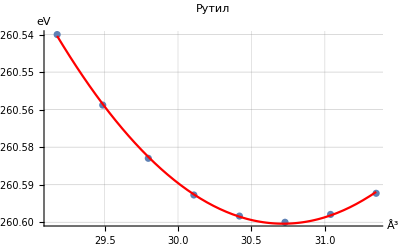

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["fplo_calc"];
SetDirectory["rutile"];
rutileCnsts=FileNames[];
(*Volume values*)
Subscript[V, r]=Quantity[ToExpression[rutileCnsts]/2,("Angstroms")^3];
(*Getting EE data*)
dataRutile=Import[#<>"/rutile0.out","Lines"]&/@rutileCnsts;
(*Selecting only last strings*)
eeLastStrRutile=Last[#]&/@(Select[#,StringMatchQ["EE:*"][#]==True&]&/@dataRutile);
(*Splitting and selecting first column*)
eeRutile=UnitConvert[Quantity[ToExpression/@(StringSplit[#,RegularExpression["\\s+"]]&/@eeLastStrRutile)[[All,2]]/2,"HartreeEnergy"],"Electronvolts"];
eeOnVR=Transpose[{Subscript[V, r],eeRutile}];
(*Fixing short tick labels*)
tck=Subdivide[
  Min[QuantityMagnitude[eeRutile]],
  Max[QuantityMagnitude[eeRutile]],
  5];
tckLabels=Transpose[{tck,ToString/@(NumberForm[#,{∞,2}]&/@tck)}];
(**Storing plot**)
eeOnVRPlot=ListPlot[eeOnVR,TargetUnits->Automatic,AxesLabel->Automatic,PlotLabel->"Рутил",Ticks->{
Automatic,
tckLabels},GridLines->Automatic];
(*Fitting curve*)
fitR=NonlinearModelFit[QuantityMagnitude@eeOnVR,a x^2+b x+c,{a,b,c},x];
(*Plotting fit*)
fitPlotR=Plot[fitR["BestFit"],{x,QuantityMagnitude@Min[Subscript[V, r]],QuantityMagnitude@Max[Subscript[V, r]]},PlotStyle->Red];
Show[eeOnVRPlot,fitPlotR]
```

Зависимость полной энергии элементарной ячейки рутила от ее объема

Параметры аппроксимации кривой EE(V) для рутила

```mathematica
fitR["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0279953 | 0.000417713 | 67.0204 | 1.40034×10^-8
b | -1.71981 | 0.0252841 | -68.0194 | 1.30057×10^-8
c | -27234.2 | 0.382439 | -71211.8 | 1.03644×10^-23

Для определения объемного модуля упругости K воспользуемся фориулой (3).

K=-V(∂P)/(∂V)

Давление задается формулой -(∂E)/(∂V)=P. По аппроксимированным функциям находим значения равновесного объема:

```mathematica
vea=Quantity[x/.Solve[D[fit["BestFit"], x]==0,x][[1]],("Angstroms")^3];
ver=Quantity[x/.Solve[D[fitR["BestFit"], x]==0,x][[1]],("Angstroms")^3];
Print["V_a≈",vea,", V_r≈",ver]
```

V_a≈33.5306 Å^3, V_r≈30.7161 Å^3

Используя данные значения находим значения объемного модуля упругости для анатаза и рутила:

```mathematica
ka=UnitConvert[-vea*Quantity[-D[fit["BestFit"], x,x],("Electronvolts")/((("Angstroms")^3)^2)],"Gigapascals"];
kr=UnitConvert[-ver*Quantity[-D[fitR["BestFit"], x,x],("Electronvolts")/((("Angstroms")^3)^2)],"Gigapascals"];
Print["K_a≈",ka, ", K_r≈",kr]
```

K_a≈264.534 GPa, K_r≈275.544 GPa

## Определение электронных свойств анатаза и рутила

### Плотность состояний и электронные свойства анатаза

Для определения электроннных свойств анатаза строим графики плотности состояний от энергии и исследуем зависимость ширины запрещенной зоны от энергии. На рисунке ниже представоены графики зависиомти электронной плотности от энергии при различных объемах.

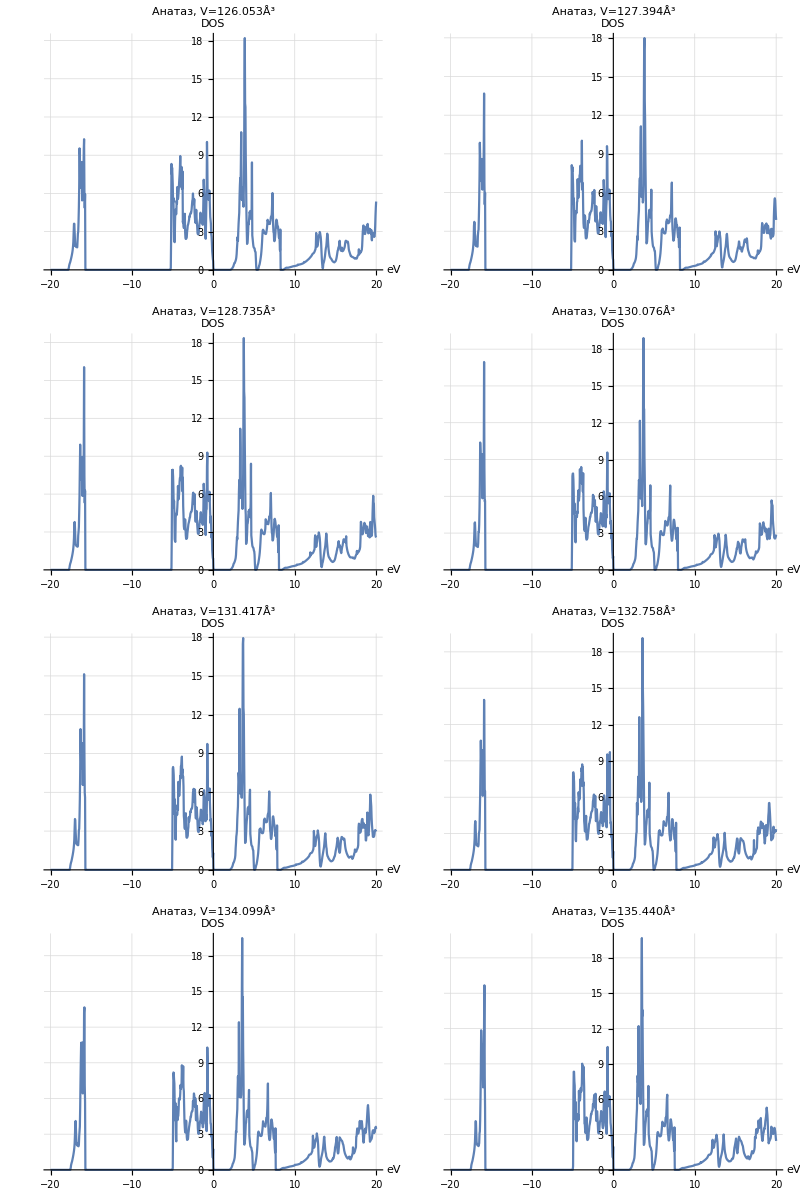

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["fplo_calc"];
SetDirectory["anatase"];
anataseCnsts=FileNames[];
dosAnatase=(Import[#<>"/+dos.total","Table"]&/@anataseCnsts)[[All,2;;1001]];
dosAnatase[[All,All,1]]=Quantity[dosAnatase[[All,All,1]],"Electronvolts"];
dosAnatasePlData=Transpose[{anataseCnsts,dosAnatase}];
dosAPlots=ListLinePlot[#[[2]],PlotRange->Full,TargetUnits->Automatic,AxesLabel->{Automatic,"DOS"},PlotLabel->"Анатаз, V="<>#[[1]]<>"Å^3",GridLines->Automatic]&/@dosAnatasePlData;
Grid[Partition[dosAPlots,2],Spacings->{1, 1}]
```

Теперь постараемся найти ширину запрещенной зоны и выявить какую-либо зависимость её от объема.

Для этого возьмем первое значение с ненулевой плотностью состояний при энергии выше нуля для каждого давления. Сами значения давления при этом используем из аппроксимации проведенной ранее.

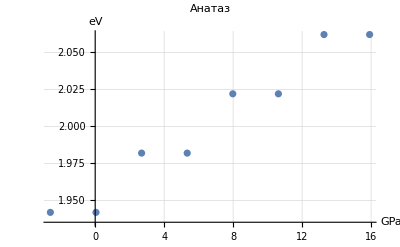

```mathematica
cc=(Quantity[c,"Electronvolts"]/.fit["BestFitParameters"]);
bc=(Quantity[b,("Electronvolts")/("Angstroms")^3]/.fit["BestFitParameters"]);
ac=(Quantity[a,("Electronvolts")/("Angstroms")^6]/.fit["BestFitParameters"]);
AnataseEOnV[x_]:=cc+bc*x+ac*x^2;
AnatasePOnV=Function[x,Evaluate[-D[AnataseEOnV[x],x]]];
bandgapOnVolumeAnatase={Quantity[ToExpression@anataseCnsts,("Angstroms")^3],(First[Select[dosAnatasePlData[[#]][[2]][[501;;750]],#[[2]]>0&]]&/@Range[8])[[All,1]]}//Transpose;
bandgapOnPressureAnatase=
{
UnitConvert[#,"Gigapascals"]&/@
(AnatasePOnV@
(bandgapOnVolumeAnatase[[All,1]]/4)
),
bandgapOnVolumeAnatase[[All,2]]
}//Transpose;
ListPlot[bandgapOnPressureAnatase,TargetUnits->Automatic,AxesLabel->Automatic,PlotLabel->"Анатаз", GridLines->Automatic]
```

При этом мы получили функцию зависимости P(V) для анатаза (единственный аргумент x соответствует объему в Å^3):

```mathematica
AnatasePOnV//TraditionalForm
```

x↦1.65109 eV/Å^3+x (-0.0492414 eV/Å^6)

### Плотность состояний и электронные свойства рутила

Аналогично предыдущему пункту строим графики плотности вероятности от энергии для рутила.

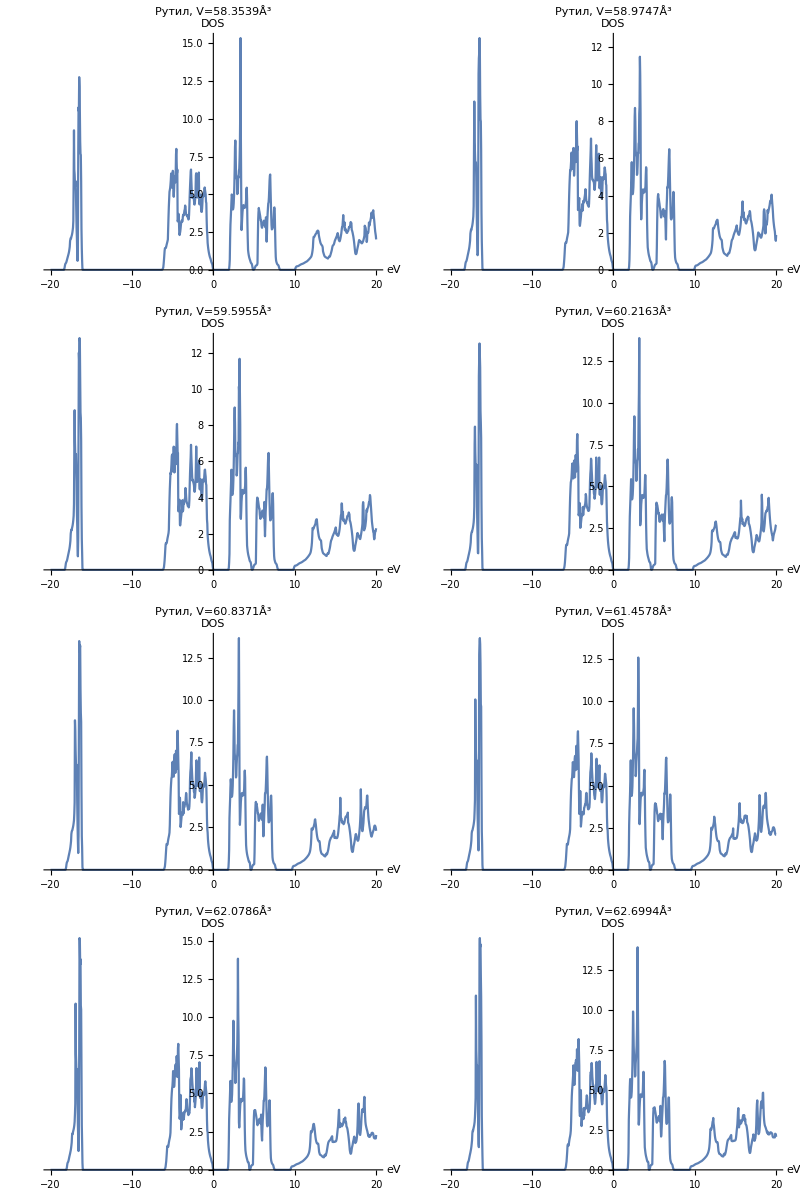

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["fplo_calc"];
SetDirectory["rutile"];
rutileCnsts=FileNames[];
dosRutile=(Import[#<>"/+dos.total","Table"]&/@rutileCnsts)[[All,2;;1001]];
dosRutile[[All,All,1]]=Quantity[dosRutile[[All,All,1]],"Electronvolts"];
dosRutilePlData=Transpose[{rutileCnsts,dosRutile}];
dosRPlots=ListLinePlot[#[[2]],PlotRange->Full,TargetUnits->Automatic,AxesLabel->{Automatic,"DOS"},PlotLabel->"Рутил, V="<>#[[1]]<>"Å^3"]&/@dosRutilePlData;
Grid[Partition[dosRPlots,2],Spacings->{1, 1}]
```

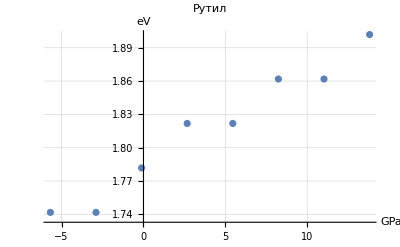

```mathematica
ccr=(Quantity[c,"Electronvolts"]/.fitR["BestFitParameters"]);
bcr=(Quantity[b,("Electronvolts")/("Angstroms")^3]/.fitR["BestFitParameters"]);
acr=(Quantity[a,("Electronvolts")/("Angstroms")^6]/.fitR["BestFitParameters"]);
RutileEOnV[x_]:=ccr+bcr*x+acr*x^2;
RutilePOnV=Function[x,Evaluate[-D[RutileEOnV[x],x]]];
bandgapOnVolumeRutile={Quantity[ToExpression@rutileCnsts,("Angstroms")^3],(First[Select[dosRutilePlData[[#]][[2]][[501;;750]],#[[2]]>0&]]&/@Range[8])[[All,1]]}//Transpose;
bandgapOnPressureRutile={
UnitConvert[#,"Gigapascals"]&/@
(RutilePOnV@
(bandgapOnVolumeRutile[[All,1]]/2)
),
bandgapOnVolumeRutile[[All,2]]
}//Transpose;
ListPlot[bandgapOnPressureRutile,TargetUnits->Automatic,AxesLabel->Automatic,PlotLabel->"Рутил", GridLines->Automatic]
```

При этом мы так же получили функцию зависимости P(V) для рутила (единственный аргумент x соответствует объему в Å^3):

```mathematica
RutilePOnV//TraditionalForm
```

x↦1.71981 eV/Å^3+x (-0.0559906 eV/Å^6)

### Давление фазового перехода

Построим зависимость E(P) для каждой фазы. Для этого рассчитаем используем ранее полученные функции P(V) и построим зависимость в явном виде. Данные расчеты проводим для анатаза.

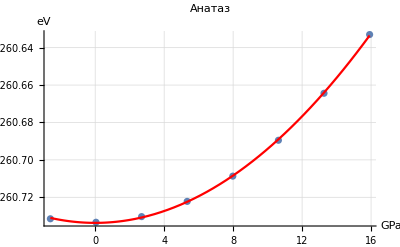

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.000395566 | 5.60441×10^-6 | 70.5812 | 1.08124×10^-8
b | -1.07926×10^-12 | 0.000080305 | -1.34395×10^-8 | 1
c | -27260.7 | 0.000270299 | -1.00854×10^8 | 1.81902×10^-39

```mathematica
AnataseEOnPData={UnitConvert[#,"Gigapascals"]&/@(eeOnVA[[All,1]]//AnatasePOnV),eeOnVA[[All,2]]}//Transpose;
AnataseEOnPPlot=ListPlot[AnataseEOnPData,TargetUnits->Automatic,AxesLabel->Automatic,PlotLabel->"Анатаз", GridLines->Automatic];
AnataseEOnPFit=NonlinearModelFit[QuantityMagnitude@AnataseEOnPData,{a x^2+b x+c},{a,b,c},x];
AnataseEOnPFitPlot=Plot[AnataseEOnPFit["BestFit"],{x,QuantityMagnitude@Min[AnataseEOnPData[[All,1]]],QuantityMagnitude@Max[AnataseEOnPData[[All,1]]]},PlotStyle->Red];
Show[AnataseEOnPPlot,AnataseEOnPFitPlot]
AnataseEOnPFit["ParameterTable"]
```

И таким образом мы получили функцию E_анатаз(P):

```mathematica
(*AnataseEOnPFitFunc[p_]:=(Quantity[a/.(AnataseEOnPFit["BestFitParameters"][[1]]),"Electronvolts"])+(Quantity[b/.(AnataseEOnPFit["BestFitParameters"][[2]]),("Electronvolts")/("Gigapascals")]*p)+(Quantity[c/.(AnataseEOnPFit["BestFitParameters"][[3]]),("Electronvolts")/("Gigapascals")^2]*p^2);*)
AnataseEOnPFitFunc[p_]:=AnataseEOnPFit["Function"]@p;
AnataseEOnPFitFunc[p]//TraditionalForm
```

0.000395566 p^2-1.07926×10^-12 p-27260.7

Дополнительно построим зависмость V(P) и проведем её аппроксимацию:

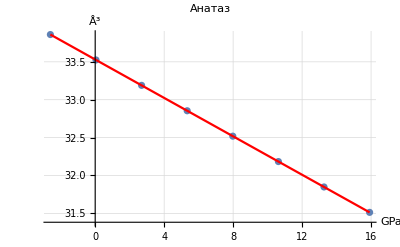

| Estimate | Standard Error | t-Statistic | P-Value
1 | 33.5306 | 9.51518×10^-15 | 3.52391×10^15 | 3.52498×10^-92
x | -0.126753 | 1.05685×10^-15 | -1.19935×10^14 | 2.2679×10^-83

```mathematica
AnataseVOnPData={UnitConvert[#,"Gigapascals"]&@(eeOnVA[[All,1]]//AnatasePOnV),eeOnVA[[All,1]]}//Transpose;
AnataseVOnPPlot=ListPlot[AnataseVOnPData,TargetUnits->Automatic,AxesLabel->Automatic,PlotLabel->"Анатаз", GridLines->Automatic];
AnataseVOnPFit=LinearModelFit[QuantityMagnitude@AnataseVOnPData,x,x];
AnataseVOnPFitPlot=Plot[AnataseVOnPFit["BestFit"],{x,QuantityMagnitude@Min[AnataseVOnPData[[All,1]]],QuantityMagnitude@Max[AnataseVOnPData[[All,1]]]},PlotStyle->Red];
Show[AnataseVOnPPlot,AnataseVOnPFitPlot]
AnataseVOnPFit["ParameterTable"]
```

Таким образом мы получили функцию V_анатаз(P):

```mathematica
(*AnataseVOnPFitFunc[p_]:=Quantity[AnataseVOnPFit["BestFitParameters"][[1]],("Angstroms")^3]+Quantity[AnataseVOnPFit["BestFitParameters"][[2]],("Angstroms")^3/("Gigapascals")]*p;*)
AnataseVOnPFitFunc[p_]:=AnataseVOnPFit["Function"]@p;
AnataseVOnPFitFunc[p]//TraditionalForm
```

33.5306-0.126753 p

Производим аналогичные построения и расчеты для рутила:

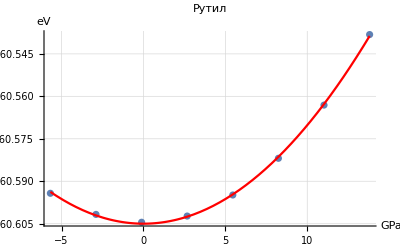

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.000347884 | 5.19072×10^-6 | 67.0204 | 1.40034×10^-8
b | -8.30231×10^-13 | 0.0000511206 | -1.62406×10^-8 | 1
c | -27260.6 | 0.000252159 | -1.08109×10^8 | 1.28527×10^-39

```mathematica
RutileEOnPData={UnitConvert[#,"Gigapascals"]&/@(eeOnVR[[All,1]]//RutilePOnV),eeOnVR[[All,2]]}//Transpose;
RutileEOnPPlot=ListPlot[RutileEOnPData,TargetUnits->Automatic,AxesLabel->Automatic,PlotLabel->"Рутил", GridLines->Automatic];
RutileEOnPFit=NonlinearModelFit[QuantityMagnitude@RutileEOnPData,{a x^2+b x+c},{a,b,c},x];
RutileEOnPFitPlot=Plot[RutileEOnPFit["BestFit"],{x,QuantityMagnitude@Min[RutileEOnPData[[All,1]]],QuantityMagnitude@Max[RutileEOnPData[[All,1]]]},PlotStyle->Red];
Show[RutileEOnPPlot,RutileEOnPFitPlot]
RutileEOnPFit["ParameterTable"]
```

E_рутил(P):

```mathematica
(*RutileEOnPFitFunc[p_]:=(Quantity[a/.(RutileEOnPFit["BestFitParameters"][[1]]),"Electronvolts"])+(Quantity[b/.(RutileEOnPFit["BestFitParameters"][[2]]),("Electronvolts")/("Gigapascals")]*p)+(Quantity[c/.(RutileEOnPFit["BestFitParameters"][[3]]),("Electronvolts")/("Gigapascals")^2]*p^2);*)
RutileEOnPFitFunc[p_]:=RutileEOnPFit["Function"]@p;
RutileEOnPFitFunc[p]//TraditionalForm
```

0.000347884 p^2-8.30231×10^-13 p-27260.6

V_рутил(P):

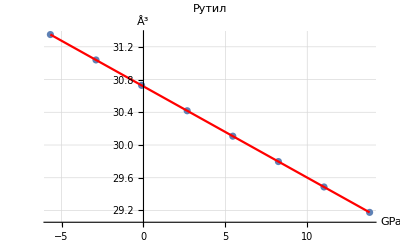

| Estimate | Standard Error | t-Statistic | P-Value
1 | 30.7161 | 3.03937×10^-15 | 1.01061×10^16 | 6.33596×10^-95
x | -0.111474 | 4.01879×10^-16 | -2.77383×10^14 | 1.48193×10^-85

```mathematica
RutileVOnPData={UnitConvert[#,"Gigapascals"]&@(eeOnVR[[All,1]]//RutilePOnV),eeOnVR[[All,1]]}//Transpose;
RutileVOnPPlot=ListPlot[RutileVOnPData,TargetUnits->Automatic,AxesLabel->Automatic,PlotLabel->"Рутил", GridLines->Automatic];
RutileVOnPFit=LinearModelFit[QuantityMagnitude@RutileVOnPData,x,x];
RutileVOnPFitPlot=Plot[RutileVOnPFit["BestFit"],{x,QuantityMagnitude@Min[RutileVOnPData[[All,1]]],QuantityMagnitude@Max[RutileVOnPData[[All,1]]]},PlotStyle->Red];
Show[RutileVOnPPlot,RutileVOnPFitPlot]
RutileVOnPFit["ParameterTable"]
```

```mathematica
(*RutileVOnPFitFunc[p_]:=Quantity[RutileVOnPFit["BestFitParameters"][[1]],("Angstroms")^3]+Quantity[RutileVOnPFit["BestFitParameters"][[2]],("Angstroms")^3/("Gigapascals")]*p;*)
RutileVOnPFitFunc[p_]:=RutileVOnPFit["Function"]@p;
RutileVOnPFitFunc[p]//TraditionalForm
```

30.7161-0.111474 p

Теперь построим зависимость изменения энтальпии от давления согласно формуле

ΔH(P)=E_рутил(P)-E_анатаз(P)+p(V_рутил (P)-V_анатаз(P))

Определив давление, при котором ΔH становится нулевой мы получим давление фазового перехода. Далее приведем график данной функции:

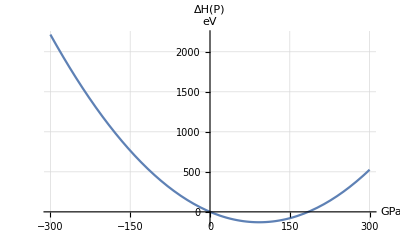

```mathematica
DeltaH[p_]:=RutileEOnPFitFunc[p]-AnataseEOnPFitFunc[p]+p(RutileVOnPFitFunc[p]-AnataseVOnPFitFunc[p]);
Plot[DeltaH[p],{p,-300, 300},PlotLabel->ΔH[P],AxesLabel->{" GPa"," eV"},GridLines->Automatic]
```

Производная становится нулевой в точке:

```mathematica
Quantity[#,"Gigapascals"]&@(p/.Solve[D[DeltaH[p],p]==0,p][[1]])
```

92.3932 GPa

Данное значение и является давлением фазового перехода. Таким образом мы получили искомые результаты.